# Broadband Network Congestion Measurement

How long as TWC been aware of network congestion in High Speed Internet service to Hana, HI?

by Chase.Turner@TFarms.com

For discussion purposes only.  Use of this report requires specific permission of the author.

## Terminology

## Implementation

#### Color Scheme for probes

```mathematica
ClearAll[colorCodeForProbe];
Block[{},
colorCodeForProbe[1165]=Blue;
colorCodeForProbe[1178]=Red;
colorCodeForProbe[2289]=Purple;
colorCodeForProbe[10546]=Brown;
];
(* TEST *)
pprintProbe/@ {1165,1178,2289,10546}
```

{pprintProbe[1165],pprintProbe[1178],pprintProbe[2289],pprintProbe[10546]}

#### PlotStyle for probe

```mathematica
ClearAll[plotStyleForProbe];
plotStyleForProbe[aProbe_Integer, pSize_, pOpacity_]:=colorCodeForProbe[aProbe];
(* TEST *)
plotStyleForProbe[1165,.001,0.5]
```

RGBColor[0,0,1]

#### Pretty Print for Probe

```mathematica
ClearAll[pprintProbe];
pprintProbe[probe_Integer]:= Style["p"<>ToString[probe],FontColor->colorCodeForProbe[probe], Plain,"Text"];
(* TEST *)
pprintProbe/@ {1165,1178,2289,10546}
```

{p1165,p1178,p2289,p10546}

## BuiltIn measurements for 1st and 2nd hop

#### Conversion of Unix Machine Timestamp to Mathematica Time

```mathematica
ClearAll[unixTimeToHST];
(* Hawaiian Timezone is -10 from GMT *)
unixTimeToHST[x_Integer]:=DateList[AbsoluteTime[{1970,1,1,2,0,0}]+x,TimeZone->-10.0];
(* TEST *)
unixTimeToHST[1330434000]
```

{2012,2,28,10,0,0.}

#### Sources

```mathematica
(* urlForPingJSONData - answer with the JSON URL for fetching data *)
ClearAll[urlForPingJSONData];urlForPingJSONData::usage = "URL to get atlas.ripe.net ping data";urlForPingJSONData::unexpectedArg="`1`";
(* IMPLEMENTATION *)urlForPingJSONData[probeID_Integer,
resolution_String /;StringMatchQ[resolution, "1h" | "1d"],
hopNumber_Integer /; MatchQ[hopNumber , 1|2] , 
startDate_String, 
endDate_String]:="https://stat.ripe.net/data/atlas-ping-measurements/data.json?probe_id="<>ToString[probeID]<>"&measurement_id="<> ToString[hopNumber]<>"&starttime="<>startDate<>"&endtime="<>endDate<>"&resolution="<>resolution;
(* UNEXPECTED ARGUMENT *)
urlForPingJSONData[probeID_,resolution_,hopNumber_, startDate_, endDate_]:= Message[urlForPingJSONData::unexpectedArg,{probeID, resolution, hopNumber, startDate,endDate}];
(* TEST *)
urlForPingJSONData[1178,"1h",1,"2012-02-24T08:19:23","2014-05-09T16:50:21"]
```

https://stat.ripe.net/data/atlas-ping-measurements/data.json?probe_id=1178&measurement_id=1&starttime=2012-02-24T08:19:23&endtime=2014-05-09T16:50:21&resolution=1h

```mathematica
(* fileForPingJSONData - answer with the JSON URL for fetching data *)
ClearAll[fileForPingJSONData];fileForPingJSONData::usage = "URL to get atlas.ripe.net ping data";fileForPingJSONData::unexpectedArg="`1`";
(* IMPLEMENTATION *)fileForPingJSONData[probeID_Integer,
resolution_String /;StringMatchQ[resolution, "1h" | "1d"],
hopNumber_Integer /; MatchQ[hopNumber , 1|2] , 
startDate_String, 
endDate_String]:=FileNameJoin[{NotebookDirectory[],"data","atlas.ripe.net-builtIn-p"<>ToString[probeID]<>"-resolution_"<>resolution<>"-hop_"<> ToString[hopNumber]<>".json"}];
(* UNEXPECTED ARGUMENT *)
fileForPingJSONData[probeID_,resolution_,hopNumber_, startDate_, endDate_]:= Message[fileForPingJSONData::unexpectedArg,{probeID, resolution, hopNumber, startDate,endDate}];
(* TEST *)
fileForPingJSONData[1178,"1h",1,"2012-02-24T08:19:23","2014-05-09T16:50:21"]
```

/Users/chase/src/git/atlas.ripe.net/builtInMetrics/data/atlas.ripe.net-builtIn-p1178-resolution_1h-hop_1.json

```mathematica
pullAndCache[probeID_Integer,resolution_String,hopNumber_Integer]:= Module[{urlHopData, cachingFile, hardCodedStart, hardCodedEnd},
hardCodedStart="2012-02-24T08:19:23";
hardCodedEnd="2014-05-09T16:50:21";
urlHopData=Import[urlForPingJSONData[probeID,resolution,hopNumber,hardCodedStart,hardCodedEnd],"JSON"];
cachingFile=fileForPingJSONData[probeID,resolution,hopNumber,hardCodedStart,hardCodedEnd];
Export[cachingFile,urlHopData,"JSON"];
urlHopData];
```

#### JSON data file

```mathematica
(* jsonData returns data portion of the data set from the local cached file, or a new data set is pulled from atlas.ripe.net, cached, and referenced *)

ClearAll[jsonData];
jsonData::usage="fetch cached json data or pull from atlas";
jsonData::unexpectedArg="`1`";
jsonData::datasetMismatch ="Args `1` do not match data property in file `2`";
(* IMPLEMENTATION *)
jsonData[probeID_Integer,resolution_String,hopNumber_Integer]:=Module[{startDate="2012-02-24T08:19:23", endDate="2014-05-09T16:50:21",jsonFile, url,jsonImport,jsonData},
jsonFile=fileForPingJSONData[probeID,resolution,hopNumber,startDate,endDate];
url=urlForPingJSONData[probeID,resolution,hopNumber,startDate,endDate];
(* TODO check local; if nothing, pull from atlas and store. With result, verify  *)
jsonImport=If[FileExistsQ[jsonFile],Import[jsonFile,"JSON"],pullAndCache[probeID, resolution, hopNumber]];
(* Walk JSON data structure, asserting with each traversal it is not null *)
Module[{jsonDataProbeID, jsonDataMeasurementID,jsonDataResolution},
jsonData="data"/. jsonImport;
Assert[jsonData!={}];
(* Assert - file matches the requested probe data *)
jsonDataProbeID= "probe_id"/.jsonData;
jsonDataMeasurementID="measurement_id" /. jsonData;
jsonDataResolution ="resolution"/. jsonData;
Assert[ToString[probeID]==jsonDataProbeID];
Assert[ToString[hopNumber]==jsonDataMeasurementID];
Assert[resolution==jsonDataResolution];
];
(* CONFIRM data set referened matches argements  *)
(* ---> returning *)
jsonData
];
(* UNEXPECTED ARGUMENT *)
jsonData[probeID_, resolution_]:=Message[jsonData::unexpectedArg, {probeID, resolution}];
(* TEST *)
```

#### jsonDataMeasurementsToCDF

```mathematica
(* jsonDataMeasurementsToCDF returns CDF version of measurementData *)

ClearAll[jsonDataMeasurementsToCDF];
jsonDataMeasurementsToCDF::usage="convert JSON data to CDF";
jsonDataMeasurementsToCDF::unexpectedArg="`1`";
(* IMPLEMENTATION *)
jsonDataMeasurementsToCDF[probeID_Integer,resolution_String,hopNumber_Integer]:=Module[{measurements, converted},
(* Traverse JSON graph to get to measurements *)
measurements="measurements"/. jsonData[probeID,resolution,hopNumber];
(* flatten and convert values where necessary *)
(* ASSERT : format is rules as the following example
{"received"-> 6, 
"rtt_5pct"->10.088,
"rtt_95pct"->21.066,
"rtt_med"->14.8675,
"sent"->6,
"timestamp"->1330434000}
 *)
(* ---> returning *)
Join[{"probe_id"->probeID,"measurement_id"->hopNumber,"resolution"->resolution},#[[1;;5]],{"timestamp"->unixTimeToHST["timestamp"/.#[[6]]]}]& /@measurements
]
(* UNEXPECTED ARGUMENT *)
jsonDataMeasurementsToCDF[probeID_, resolution_]:=Message[jsonDataMeasurementsToCDF::unexpectedArg, {probeID, resolution}];
(* TEST *)
Dimensions[jsonDataMeasurementsToCDF[1178,"1h",1]]
```

{18600,9}

#### Combine Measurements to tMeasurements

```mathematica
ClearAll[tMeasurements];
tMeasurements=Join[
jsonDataMeasurementsToCDF[1165,"1h",1],
jsonDataMeasurementsToCDF[1178,"1h",1],
jsonDataMeasurementsToCDF[2289,"1h",1],
jsonDataMeasurementsToCDF[10546,"1h",1],
jsonDataMeasurementsToCDF[1165,"1h",2],
jsonDataMeasurementsToCDF[1178,"1h",2],
jsonDataMeasurementsToCDF[2289,"1h",2],
jsonDataMeasurementsToCDF[10546,"1h",2]
];
Dimensions[tMeasurements]
```

{117959,9}

```mathematica
exportToCSV[dataSet_List]:=Module[{header,distilledData},
header={"timestamp","probe_id","measurement_id","resolution","rtt_med","rtt_5pct","rtt_95pct"};
distilledData=header /. dataSet;
Export["/tmp/atlas.ripe.net.builtInMetrics.csv",Join[{header},Join[{DateString[#[[1]]]},#[[2;;]]]&/@distilledData],"CSV"]
"Look for export in /tmp/atlas.ripe.net.builtInMetrics.csv"
];
exportToCSV[tMeasurements];
```

```mathematica
Dimensions[Cases[tMeasurements,
{"probe_id"->probeID_,
"measurement_id"->measurementID_,
"resolution"->resolution_,
"received"->received_,
"rtt_5pct"-> rtt5pct_,
"rtt_95pct"->rtt95pct_,
"rtt_med"->rttMed_,
"sent"->sent_,
"timestamp"->timestamp_}]]
```

{117959,9}

#### tMeasurements to tMeasurementsAsCDF

```mathematica
(* MAGIC ORDINAL ALERT : from this point on, static awareness of this structure is presumed, meaning you are keeping track of the ordinal offset to desired properties *)

tMeasurementsAsCDF={"timestamp","probe_id","measurement_id","resolution","rtt_med","rtt_5pct","rtt_95pct","sent","received"}/. tMeasurements;
```

```mathematica
Dimensions[tMeasurements]==Dimensions[tMeasurementsAsCDF]
```

True

## Analysis of tMeasurements

#### Profiles of various data values

```mathematica
(* In regards to rtt data sent and received, what value is most frequent? *)
{#,BinCounts[#/.tMeasurements,{0,100,10}]}&/@{"sent","received"}//MatrixForm
```

(sent | {156,184,272,2175,114058,966,147,1,0,0}
received | {156,184,272,2175,114058,966,147,1,0,0})

```mathematica
(* For first Hop Only, please plot rtt_med *)
```

```mathematica
selectElements[list_,start_,end_]:=Module[{s=AbsoluteTime@start,e=AbsoluteTime@end},Select[list,Composition[s≤#≤e&,AbsoluteTime,First]]]
```

```mathematica
ClearAll[rttMatch];
rttMatch[dataSet_List,returnMatchOnlyP_,requiredArgs_List]:=
Block[{probesV,hoursListV,intervalRttMedV,hopV,matches},
{probesV,hoursListV,intervalRttMedV,hopV}={"probes","List[hours]","Interval[rtt_med]","hop"}/. requiredArgs;


matches=
Cases[dataSet,
{"probe_id"->probeID_/; probeID==#,
"measurement_id"->measurementID_/; measurementID==hopV,
"resolution"->resolution_,
"received"->received_,
"rtt_5pct"-> rtt5pct_,
"rtt_95pct"->rtt95pct_,
"rtt_med"->rttMed_,
"sent"->sent_,
"timestamp"->timestamp_
}:>{timestamp,rttMed}/; If[returnMatchOnlyP,
And[
IntervalMemberQ[intervalRttMedV,rttMed],
MemberQ[hoursListV,timestamp[[4]]]
],
True]
]&/@probesV;
(* ---> RETURNING *)
matches
];
```

## Visualization

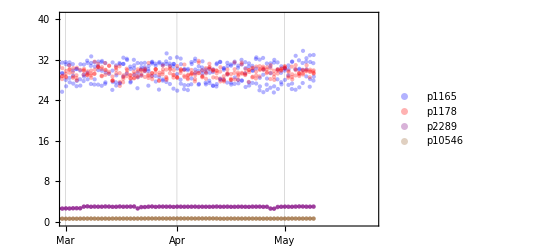
-Graphics-HOP 1 for hours {0, 1, 2, 3}avg 1h RTT ( ms )

```mathematica
ClearAll[rttMedVisualization];

rttMedVisualization[probes_,hop_,hourOfDay_List,rttInterval_Interval, dateRange_]:=
Block[
{

pointSize=Tiny,
pointOpacity=0.3,

matchesIncludingNulls,
dataToVisualize
},

matchesIncludingNulls=rttMatch[
tMeasurements,
True,
{"probes"->probes,
"hop"->hop,
"Interval[rtt_med]"->rttInterval,
"List[hours]"-> hourOfDay
}];

(* MAGIC - Replace null values with one negative valued data point *)
dataToVisualize = matchesIncludingNulls /. {}->{DateList[],-1};

Labeled[
DateListPlot[
dataToVisualize,
PlotStyle->Flatten[{{colorCodeForProbe[#], PointSize[pointSize],Opacity[pointOpacity]}}&/@probes,1],
PlotLegends->Placed[PointLegend[pprintProbe/@probes],Bottom],
PlotRange-> {dateRange,{Min[rttInterval],Max[rttInterval]}}
],
{"HOP "<> ToString[hop] <> " for hours "<>ToString[hourOfDay],"avg 1h RTT ( ms )"},{Bottom,Left},RotateLabel->True
]];

rttMedVisualization[{1165,1178,2289,10546},1,Range[0,3],Interval[{0.0,40.5}],{DateList[{2014,3,1}],DateList[]}]
```

```mathematica
Table[ListAnimate[Table[
rttMedVisualization[{1165,1178,2289,10546},hop,Range[hour,hour],Interval[{0.0,40.5}],{DateList[{2012,3,1}],DateList[]}],{hour,0,23}]],{hop,1,2}]
```

{,}

#### Scratch

```mathematica
(* SCRATCH*)
```

```mathematica
fakedata=Transpose@{DatePlus[{2001,1},{#,"Month"}]&/@Range[0,99],Accumulate[RandomVariate[NormalDistribution[0,1],{100}]]-2};

Manipulate[DateListPlot[fakedata,Joined->False,PlotRange->{{start,end},Automatic}],{start,AbsoluteTime@{2000,12},AbsoluteTime@{2004,6}},{end,AbsoluteTime@{2005,6},AbsoluteTime@{2009}}]
```